## sigma from relaxation time approx with constant τ

```mathematica
style={Directive[Darker[Blue], Thick],Directive[Orange,Thick,Dashed],Directive[Cyan,Thick,Dashing[0.02]]};

Clear[sig,s,μ,B,v0];
sig[B_,μ_,v0_,βintra11_,{s_,sm_}]:=Block[{e=1,bc1,θ,kf1,ϕ=0,vvec1,vmm1,vdotk1,vdotk2,conteq,Dphase1,vz1,s1,int1},
kf1[θ_]=(μ+√(μ^2-2 B e sm v0^2 Cos[θ]))/(2 v0);
bc1[θ_]=-s/( kf1[θ])^2{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase1[θ_]=1 +e {0,0,B}.bc1[θ] (*-Graphics-*);
vvec1[θ_]=s v0{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm1[θ_]=(-  sm B e v0)/( kf1[θ])^2{Cos[ϕ] Sin[2θ],Sin[2θ] Sin[ϕ], Cos[2 θ]};
vdotk1[θ_]=v0 (s-(B e sm Cos[θ])/kf1[θ]^2) kf1[θ];
int1[θ_]=-(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]]( s v0 Cos[θ]-(sm B e v0 Cos[2 θ])/( kf1[θ])^2+ e B(bc1[θ].(vvec1[θ]+vmm1[θ])) )^2 1/Dphase1[θ];
s1=NIntegrate[int1[θ],{θ,0,π}];
{B,s1}
];
mu=10.0^-1;v0val= 6 10^-4;in=1/16;bval=1;
sig[bval,mu,v0val,in,{3/2,3/4}]//Quiet
```

{1,-16.6667}

```mathematica
Clear[sigm0,s,μ,B,v0];(* no OMM*)
sigm0[B_,μ_,v0_,βintra11_,s_]:=Block[{e=1,sm=0,bc1,θ,kf1,ϕ=0,vvec1,vmm1,vdotk1,vdotk2,conteq,Dphase1,vz1,s1,int1},
kf1[θ_]=μ/v0;
bc1[θ_]=-s/( kf1[θ])^2{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase1[θ_]=1 +e {0,0,B}.bc1[θ];
vvec1[θ_]=s v0{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm1[θ_]=0{Cos[ϕ] Sin[2θ],Sin[2θ] Sin[ϕ], Cos[2 θ]};
vdotk1[θ_]=v0 (s-(B e sm Cos[θ])/kf1[θ]^2) kf1[θ];

int1[θ_]=-(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]]( s v0 Cos[θ]+ e B(bc1[θ].(vvec1[θ])) )^2 1/Dphase1[θ];
s1=NIntegrate[int1[θ],{θ,0,π}];
{B,s1}
];
mu=10.0^-1;v0val= 6 10^-4;in=1/16;bval=10;
sigm0[bval,mu,v0val,in,3/2]//Quiet
```

{10,-16.6667}

```mathematica
sigm0[0,mu,v0val,in,1/2]
sig[0,mu,v0val,in,{1/2,7/4}]
```

{0,-5.55556}

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{0,0.}

```mathematica
Clear[sig0,s,μ,B,v0];(* B=0 -> Drude*)
sig0[μ_,v0_,βintra11_,s_]:=Block[{e=1,sm=0,B=0,θ,kf1,ϕ=0,vvec1,vmm1,vdotk1,vdotk2,conteq,Dphase1,vz1,s1,int1},
kf1[θ_]=μ/v0;
Dphase1[θ_]=1 ;
vvec1[θ_]=s v0{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm1[θ_]=0{Cos[ϕ] Sin[2θ],Sin[2θ] Sin[ϕ], Cos[2 θ]};
vdotk1[θ_]=v0  s kf1[θ];
int1[θ_]=-(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]](s v0 Cos[θ])^2;
s1=NIntegrate[int1[θ],{θ,0,π}];
{B,s1}
];
mu=10.0^-1;v0val= 6 10^-4;in=1/16;bval=10;
sig0[mu,v0val,in,3/2]//Quiet
```

{0,-16.6667}

## data

```mathematica
mu=10.0^-1;v0val= 6 10^-3;in=1;
x1=1/Quiet[sig0[mu,v0val,in,1/2]][[2]];
x2=1/Quiet[sig0[mu,v0val,in,3/2]][[2]];
list1=Sort[Table[Quiet[sig[B,mu,v0val,in,{1/2,7/4}]],{B,-45,45,10}]];
list2=Sort[Table[Quiet[sig[B,mu,v0val,in,{3/2,3/4}]],{B,-45,45,10}]];
len=Length[list1];
dat01=Table[{list1[[i,1]],(Re[list1[[i,2]]]x1 -1)10^0},{i,1,len}];
dat02=Table[{list2[[i,1]],(Re[list2[[i,2]]]x2-1)10^0},{i,1,len}];
(*ListLinePlot[dat01]
ListLinePlot[dat02]*)
```

```mathematica
mu=10.0^-1;v0val= 6 10^-3;in=1;(* OMM off*)
x1=1/Quiet[sig0[mu,v0val,in,1/2]][[2]];
x2=1/Quiet[sig0[mu,v0val,in,3/2]][[2]];
list1=Sort[Table[Quiet[sigm0[B,mu,v0val,in,1/2]],{B,-45,45,10}]];
list2=Sort[Table[Quiet[sigm0[B,mu,v0val,in,3/2]],{B,-45,45,10}]];
len=Length[list1];
dat11=Table[{list1[[i,1]],(Re[list1[[i,2]]]x1-1)10^0},{i,1,len}];
dat12=Table[{list2[[i,1]],(Re[list2[[i,2]]]x2-1)10^0},{i,1,len}];
(*ListLinePlot[dat11]
ListLinePlot[dat12]*)
```

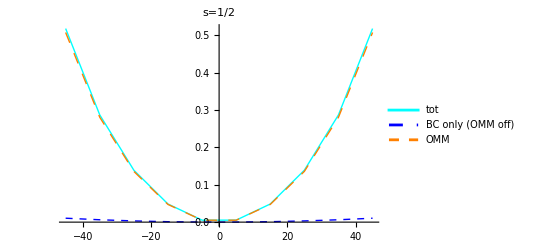

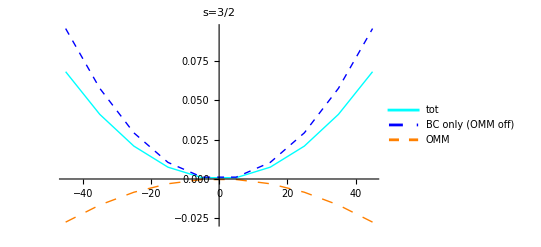

```mathematica
len=Length[list1];
dat21=Table[{list1[[i,1]],dat01[[i,2]]-dat11[[i,2]]},{i,1,len}];
dat22=Table[{list2[[i,1]],dat02[[i,2]]-dat12[[i,2]]},{i,1,len}];
ListLinePlot[{dat01,dat11,dat21},PlotLegends->{"tot","BC only (OMM off)","OMM"},PlotStyle->{Directive[Cyan, Thick],Directive[Blue,Thick,Dashed],Directive[Orange,Thick,Dashing[0.02]]},PlotLabel->"s=1/2"]

ListLinePlot[{dat02,dat12,dat22},PlotLegends->{"tot","BC only (OMM off)","OMM"},PlotStyle->{Directive[Cyan, Thick],Directive[Blue,Thick,Dashed],Directive[Orange,Thick,Dashing[0.02]]},PlotLabel->"s=3/2"]
```

## using Firdous paper formula

```mathematica
Clear[B,v0,gs,s,ups,sigzz, σzz,μ,drude,diff];
(* -Graphics-; -Graphics- *)
ups[n_]=μ^n;

(* For single band *)
v0val= 6 10^-3;τ=150;e=1;
drude[μ_,s_]=(e^2 τ)/(6 π^2 s v0val)ups[2];
sigzz[Bz_,μ_,{s_,gs_}]=drude[μ,s]+(e^4 τ  s  v0val^3 ups[-2])/(30 π^2)Bz^2 (8 s^4-9 s^2 gs + 5 gs^2);
diff[Bz_,μ_,{s_,gs_}]=drude[μ,s]+sigzz[Bz,μ,{s,gs}]-sigzz[Bz,μ,{s,0}];
```

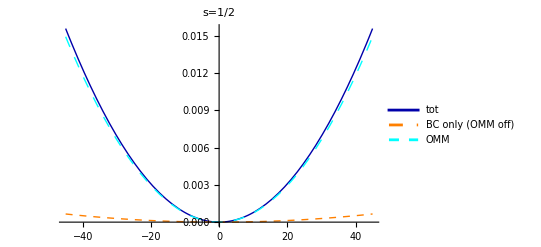

```mathematica
mu=10.0^-1;x=drude[mu,1/2];
Plot[{sigzz[B,mu,{1/2,7/4}]/x-1, (**)sigzz[B,mu,{1/2,0}]/x-1,(**)diff[B,mu,{1/2,7/4}]/x-1},{B,-45,45},PlotLabel->"s=1/2",PlotStyle->style,PlotLegends->{"tot","BC only (OMM off)","OMM"}]
```

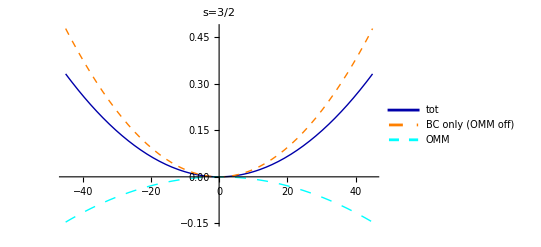

```mathematica
style={Directive[Darker[Blue], Thick],Directive[Orange,Thick,Dashed],Directive[Cyan,Thick,Dashing[0.02]]};mu=10.0^-1;x=drude[mu,3/2];
Plot[{sigzz[B,mu,{3/2,3/4}]/x-1, (**)sigzz[B,mu,{3/2,0}]/x-1,(**)diff[B,mu,{3/2,3/4}]/x-1},{B,-45,45},PlotLabel->"s=3/2",PlotStyle->style,PlotLegends->{"tot","BC only (OMM off)","OMM"}]
```

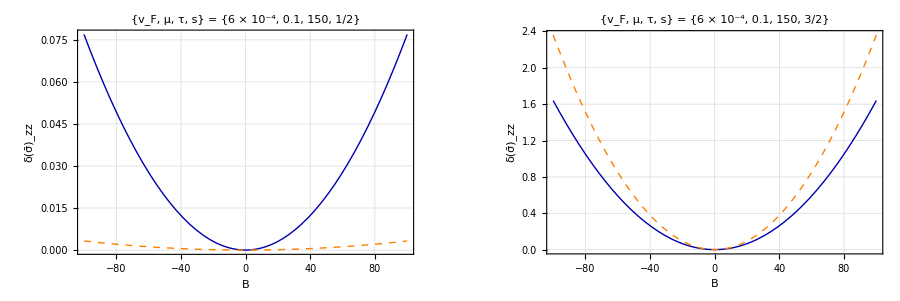

```mathematica
style={Directive[Darker[Blue], Thick],Directive[Orange,Thick,Dashed],Directive[Cyan,Thick,Dashing[0.02]]};mu=10.0^-1;x=drude[mu,1/2];
g1=Plot[{sigzz[B,mu,{1/2,7/4}]/x-1, (**)sigzz[B,mu,{1/2,0}]/x-1},{B,-100,100},FrameTicksStyle->Directive[Darker[Gray],16],PlotRange->{{-100,100},All},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,Axes->False,FrameLabel->{"B","δ(σ̄)_zz"},FrameTicksStyle->Directive[Bold,Black,12],PlotLabel->Style["{v_F, μ, τ, s} = {6 × 10^-4, 0.1, 150, 1/2}",Bold,Darker[Brown],18,FontFamily->"Times"],ImageSize->450,GridLines->Automatic];

x=drude[mu,3/2];
g2=Plot[{sigzz[B,mu,{3/2,3/4}]/x-1, (**)sigzz[B,mu,{3/2,0}]/x-1},{B,-100,100},FrameTicksStyle->Directive[Darker[Gray],16],PlotRange->{{-100,100},All},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,Axes->False,FrameLabel->{"B","δ(σ̄)_zz"},FrameTicksStyle->Directive[Bold,Black,12],PlotLabel->Style["{v_F, μ, τ, s} = {6 × 10^-4, 0.1, 150, 3/2}",Bold,Darker[Brown],18,FontFamily->"Times"],ImageSize->450,GridLines->Automatic];

leg=LineLegend[style,{"full", "OMM off"},LabelStyle->{16,Darker[Brown],Bold,FontFamily->"Times"},LegendLayout->{"Row",1}];

pl=Legended[GraphicsGrid[{{g1,g2}},Spacings->{40,0},ImageSize->900],Placed[leg,Below]]

SetDirectory[NotebookDirectory[]];
Export["sigRTA.pdf",Rasterize[pl],ImageResolution->1000];
```

```mathematica
5gs-9s^2/.{s->1/2,gs->7/4}
5gs-9s^2/.{s->3/2,gs->3/4}
```

13/2

-33/2